```mathematica
(* Lecture 7: More on controls. Midterm exam prep (Google's Version) *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,VectorPlot, VectorPlot3D,StreamPlot,RevolutionPlot3D,ContourPlot3D, Graphics3D}, BaseStyle->{16,FontFamily->"DEKCEB+GreenMarker-Regular"},ImageSize->Medium];
```

```mathematica
(* L7 demonstrates the variety of controls on a graph of f[x,y,a] , where a is the animation parameter *)
```

```mathematica
(* Define *)
```

```mathematica
f[x_,y_,a_]:=Exp[-a(x^2+y^2)]
```

```mathematica
(* Check *)
```

```mathematica
Plot3D[f[x,y,1],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Interactive plot *)
```

```mathematica
plotf[color_,a_]:=Plot3D[f[x,y,a],{x,-1,1},{y,-1,1}, PlotStyle->color,Mesh->True, MeshStyle->Yellow, PlotPoints->35]
```

```mathematica
(* The animation parameter {a,1,5,1}*)
```

```mathematica
(* Slider. Note Appearance-> "Labeled"  *)
```

```mathematica
S1:={Slider[Dynamic[a1],{1,5,1}],Dynamic[a1]}
```

```mathematica
{S1,Dynamic[plotf[Blue,a1]]}
```

{{,},}

```mathematica
(* Toggler *)
```

```mathematica
ListT2=Range[5]
```

{1,2,3,4,5}

```mathematica
(* Toggler with step 0.5 *)
```

```mathematica
ListT2=Table[i,{i,1,5,0.5}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
(* Toggler *)
```

```mathematica
T2:=Toggler[Dynamic[a2],ListT2,Background->Blue, BaseStyle->White]
```

```mathematica
{T2,Dynamic[plotf[Blue,a2]]}
```

{,}

```mathematica
(* RadioButtonBar *)
```

```mathematica
RB3:=RadioButtonBar[Dynamic[a3],ListT2]
```

```mathematica
{RB3,Dynamic[plotf[Blue,a3]]}
```

{ | 1.   | 1.5   | 2.   | 2.5   | 3.   | 3.5   | 4.   | 4.5   | 5.,}

```mathematica
(* SetterBar *)
```

```mathematica
SB4:=SetterBar[Dynamic[a4],ListT2]
```

```mathematica
{SB4, Dynamic[plotf[Blue,a4]]}
```

{ |  |  |  |  |  |  |  | ,}

```mathematica
(* Control, step is automatic *)
```

```mathematica
C5:=Control[{a5,1,5}]
```

```mathematica
{C5,Dynamic[plotf[Blue,a5]]}
```

{,}

```mathematica
(* PopMenu *)
```

```mathematica
ListT2=Range[5]
```

{1,2,3,4,5}

```mathematica
PM6:=PopupMenu[Dynamic[a6],ListT2]
```

```mathematica
{PM6,Dynamic[plotf[Blue,a6]]}
```

{,}

```mathematica
(* PopMenu: menu titles *)
```

```mathematica
PM6N:=PopupMenu[Dynamic[a7],{1->"one",2->"two",3->"three",4->"four",5->"five"}]
```

```mathematica
{PM6N,Dynamic[plotf[Blue,a7]]}
```

{,}

```mathematica
(* Let us change the animation parameter and the color 
Let us use the following combinations
1) Toggler-ColorSlider   
  2) SetterBar-PopupMenu
    3) Manipulate-Popmenu in the body of Manipulate 
      4) Manipulate: the parameters in the body     
*)
```

```mathematica
(* Toggler-ColorSlider  *)
```

```mathematica
(* Borrow T2 from example 2 *)
```

```mathematica
(* ColorSlider (new) *)
```

```mathematica
CS7=ColorSlider[Dynamic[color7]];
```

```mathematica
{T2,CS7, Dynamic[plotf[color7,a2]]}
```

{,$CellContext`color7,}

```mathematica
(*  PopMenu and Manipulate *)
```

```mathematica
ColorListGraph=RandomColor[10];
```

```mathematica
color8=ColorListGraph[[1]];
```

```mathematica
f8[x_,y_,k1_,k2_]:=Sin[k1*x*y]*Exp[-0.1k2(x^2-y^2)]
```

```mathematica
plot8[k1_,k2_,C_]:=Plot3D[f8[x,y,k1,k2],{x,-1,1},{y,-1,1},PlotStyle->C,PlotRange->1.5]
```

```mathematica
PM8:={Text["Select colorG->"], PopupMenu[Dynamic[color8],ColorListGraph]}
```

```mathematica
(* PM8 and Manipulate in one block {} *)
```

```mathematica
{Manipulate[plot8[k1,k2,color8],{k1,-1,1,0.25},{k2,-5,5,0.1}],PM8}
```

{,{Select colorG->,}}

```mathematica
(* Manipulate with 3 controls *)
```

```mathematica
Manipulate[plot8[k1,k2,C],{k1,{1,3,5,6}},{k2,-5,5,0.1},{C,ColorListGraph}]
```

```mathematica
(* Moving a cube the line between p1 and p2 *)
```

```mathematica
(* Move a triangle along the line through points p1={1,1,1}, p2={3,4,5}. ,3)  *)
```

```mathematica
(* Points *)
```

```mathematica
pp1:={1,1,1}; pp2:={3,4,5};
```

```mathematica
(* Line *)
```

```mathematica
LL[t_]:=(1-t)pp1+t pp2
```

```mathematica
GLL=ParametricPlot3D[LL[t],{t,0,1},BoxRatios->1]
```

-Graphics3D-

```mathematica
Tri[t_]:={Triangle[{LL[t]+{0,0,0},LL[t]+{1,0,0},LL[t]+{0,1,1}}]}
```

```mathematica
STri[t_]:=Graphics3D[{Red,Tri[t]}]
```

```mathematica
SAll[t_]:=Show[GLL,STri[t]]
```

```mathematica
Manipulate[SAll[t],{t,0,1}]
```

```mathematica
(* Slider2D.  *)
```

```mathematica
(* Recall a circle with the radius R and center at x0,y0. It is given by (memorize)  *)
```

```mathematica
R:=1.5
```

```mathematica
xc[t_]:=R Cos[t]
```

```mathematica
yc[t_]:=R Sin[t]
```

```mathematica
Circ[t_,x0_,y0_]:={xc[t],yc[t]}+{x0,y0}
```

```mathematica
PlotC[x0_,y0_]:=ParametricPlot[Circ[t,x0,y0],{t,0,2 Pi}, PlotRange->{{0,10},{0,10}}]
```

```mathematica
(* Check  *)
```

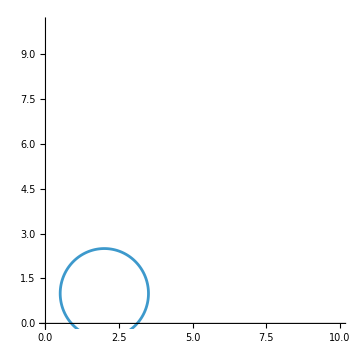

```mathematica
PlotC[2,1]
```

```mathematica
z={0,0}
```

{0,0}

```mathematica
(* Slider2D controls the position of an object in the (x,y)-plane x=z[[1],y=z[[2]]. Note Appearance-> "Labeled" *)
```

```mathematica
{Slider2D[Dynamic[z],{{0,0},{10,10}}, Background->Blue,ImageSize->Large,Appearance-> "Labeled"],Dynamic[PlotC[z[[1]],z[[2]]]]}
```

{,}

```mathematica
Options[Slider2D];
```

```mathematica
(* Design a 3D control of a sphere using Slider2D and the Vertical Slider for the z coordinate  *)
```

```mathematica
RS10=3
```

3

```mathematica
Sphere10[p_]:=Graphics3D[{Red,Opacity[0.5],Sphere[p,RS10]},Axes->True,PlotRange->-10]
```

```mathematica
(* Check  *)
```

```mathematica
Sphere10[{1,1,1}]
```

-Graphics3D-

```mathematica
S2={Slider2D[Dynamic[xy2],{{-10,-10},{10,10}}, Background->White,ImageSize->Large],Dynamic[xy2]}
```

{,}

```mathematica
SV2={VerticalSlider[Dynamic[z2],{-10,10},Background->LightBlue],Dynamic[z2]}
```

{,}

```mathematica
SphereControl={Dynamic[Sphere10[{xy2[[1]],xy2[[2]],z2}]],S2,SV2}
```

{,{,},{,}}

```mathematica
(* Below are examples of the midterm exam problems for preparation this week. 
Some of them might be considered at the lecture if the time allows *)
```

```mathematica
(* MT-Examples  *)
```

```mathematica
(* MT0 *)
```

```mathematica
(* E0 Superimpose an explicit plot and a parametric plot on one graph and a space curve.
The explicit surface is given by 
f0=4Sin[#1#2/10]&
{x,0,8},{y,0,8} 
The parametric surface is given by 
x0[u_,v_]:=Cos[v] Sin[u]
  y0[u_,v_]:=Cos[v] Cos[u]
  z0[u_,v_]:=3Sin[v^2/10]
{u,-Pi,Pi},{v,-Pi,Pi},
The space curve is given by 
xs0[t_]:=t
  ys0[t_]:=1/t
  zs0[t_]:=Sin[2t]
   {t,0,8} *)
```

```mathematica
f0=4Sin[#1#2/10]&;
```

```mathematica
P0E=Plot3D[f0[x,y] ,{x,0,8},{y,0,8} ,PlotStyle->{Blue,Opacity[0.5]},Mesh->False];
```

```mathematica
x0[u_,v_]:=Cos[v] Sin[u]
```

```mathematica
y0[u_,v_]:=Cos[v] Cos[u]
```

```mathematica
z0[u_,v_]:=3Sin[v^2/10]
```

```mathematica
p0[u_,v_]:=2{x0[u,v],y0[u,v],z0[u,v]}+{4,4,0}
```

```mathematica
P0=ParametricPlot3D[p0[u,v],{u,-Pi,Pi},{v,-Pi,Pi},PlotStyle->Green,ImageSize->Tiny];
```

```mathematica
Clear[C0,t]
```

```mathematica
xs0[t_]:=t
```

```mathematica
ys0[t_]:=1/t
```

```mathematica
zs0[t_]:=Sin[2t]
```

```mathematica
C0[t_]:={xs0[t],ys0[t],zs0[t]}
```

```mathematica
P0S:=ParametricPlot3D[C0[t],{t,0,4Pi},PlotStyle->{Red,Thickness[0.025]},BoxRatios->1]
```

```mathematica
Show[{P0E,P0,P0S}]
```

-Graphics3D-

```mathematica
(* MT1 Write a code to animate a circle moving along a 2D spiral in 2D  space. 
The color of the circle is controlled by 
 ColorList:={Red,Blue,Green}  *)
```

```mathematica
RE1:=1.5
```

```mathematica
SE1[t_]:={t Cos[t], t Sin[t]}
```

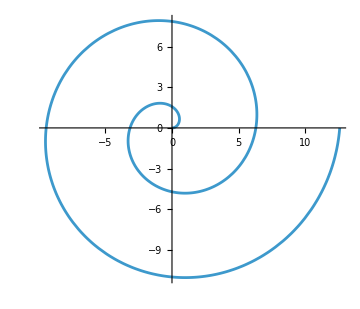

```mathematica
PathE1=ParametricPlot[SE1[t], {t,0,4Pi}]
```

```mathematica
CircleE1[t_,ColorC_]:=Graphics[{ColorC,Thick,Circle[SE1[t],RE1]}]
```

```mathematica
ColorList:={Red,Blue,Purple}
```

```mathematica
Manipulate[Show[PathE1,CircleE1[t,C]],{t,0,4Pi},{C,ColorList}]
```

```mathematica
(* MT2 Write a code to animate a circle growing in the xy plane 
(z=0)in the 3D coordinate system. 
The center of the circle is at {2,3,0}
Show the plane Z=0. Show the point {2,3,0} *)
```

```mathematica
Zero=Plot3D[0,{x,-10,10},{y,-10,10},PlotStyle->Black,BoxRatios->1]
```

-Graphics3D-

```mathematica
Cir[t_,R_]:={R Cos[t],R Sin[t],0}+{2,3,0}
```

```mathematica
Cir3D[R_]:=ParametricPlot3D[Cir[t,R],{t,0, 2Pi},PlotStyle->{Red,Thickness[0.025]}]
```

```mathematica
PointE2=Graphics3D[{Yellow,PointSize[0.04],Point[{2,3,0}]}];
```

```mathematica
AllE2[R_]:=Show[Zero,Cir3D[R],PointE2]
```

```mathematica
Manipulate[AllE2[R],{R,2,5,1}]
```

```mathematica
(* MT3 Consider a surface f1:=Exp[Sin[#1 #2]]& {u,-2,2},{v,-2,2}. 
Select two arbitrary points on the surface. Connect them by a curve lying on f1  *)
```

```mathematica
Clear[f1,P1,C1] (* not required in the mt paper *)
```

```mathematica
f1:=Exp[Sin[#1 #2]]&
```

```mathematica
(* Convert f1 into a parametric plot f1p *)
```

```mathematica
f1p:={#1,#2,f1[#1,#2]}&
```

```mathematica
P1Surface=ParametricPlot3D[f1p[u,v],{u,-2,2},{v,-2,2}]
```

-Graphics3D-

```mathematica
Clear[t] (* not required for the mt paper *)
```

```mathematica
u1=-2;u2=2;
```

```mathematica
v1=-2;v2=2;
```

```mathematica
Lu[t_]:=u1(1-t)+u2 t
```

```mathematica
Lv[t_]:=v1(1-t)+v2 t
```

```mathematica
myLine[t_]:={Lu[t],Lv[t]}
```

```mathematica
CurveL[t_]:=f1p[Lu[t],Lv[t]]
```

```mathematica
GCurveL:=ParametricPlot3D[CurveL[t],{t,0,1},PlotStyle->{Red, Thickness[0.02]}]
```

```mathematica
Show[{P1Surface,GCurveL}]
```

-Graphics3D-

```mathematica
(* MTE4(Bonus problem- at the lecture). Write a code to animate a revolution plot 
with the base curve Sin[x], {x,-a Pi/2,a Pi/2}, {a,1,3,0.25}. 
Insert the plot into a transparent sphere (LightBlue)  *)
```

```mathematica
fb[x_]:=Sin[x]
```

```mathematica
Base[a_]:=Plot[fb[x],{x,-a Pi/2,a Pi/2},PlotRange->1.5] (* illustration of fb[x], not required in the mt paper *)
```

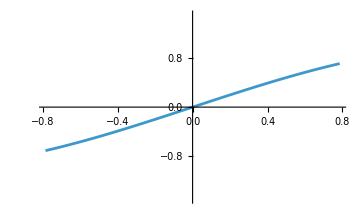
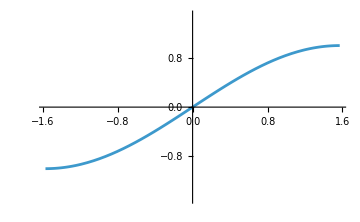
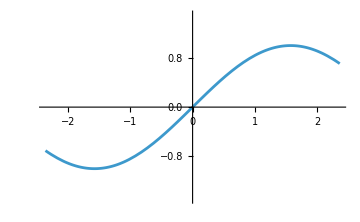
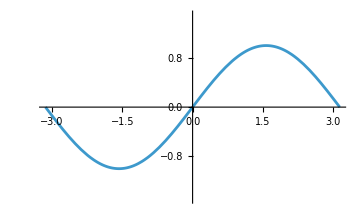

```mathematica
T=Table[Base[a],{a,0.5,2,0.5}](* illustration of fb[x], not required in the mt paper *)
```

```mathematica
RevPlot[a_]:=RevolutionPlot3D[fb[x],{x,-a Pi/2,a Pi/2},PlotRange->3,BoxRatios->1,Mesh->True]
```

```mathematica
Manipulate[RevPlot[a],{a,0.5,2,0.5}]
```

```mathematica
(* MTE5 Move a sphere R=3 along the Trefoil knot given by 
{Sin[#1]+2 Sin[2 #1],Cos[#1]-2 Cos[2 #1],-Sin[3 #1]}& {t,0, 2Pi}  *)
```

```mathematica
knot12:={Sin[#1]+2 Sin[2 #1],Cos[#1]-2 Cos[2 #1],-Sin[3 #1]}&
```

```mathematica
Tref1=ParametricPlot3D[knot12[t],{t,0,2 Pi},PlotStyle->{Blue,Thickness[0.015]}]
```

-Graphics3D-

```mathematica
(* Sphere *)
```

```mathematica
RS=0.5;
```

```mathematica
(* Sphere *)
```

```mathematica
GSphere12[t_]:=Graphics3D[{color12,Sphere[knot12[t],RS]}]
```

```mathematica
(* ColorSlider *)
```

```mathematica
CS12=ColorSlider[Dynamic[color12]]
```

$CellContext`color12

```mathematica
(* Knot *)
```

```mathematica
Gknot12=ParametricPlot3D[knot12[t],{t,0,24},PlotRange->3]
```

-Graphics3D-

```mathematica
(* Show, Dynamic *)
```

```mathematica
GAll12[t_]:=Dynamic[Show[{Gknot12,GSphere12[t]},Axes->True]]
```

```mathematica
(* Check *)
```

```mathematica
GAll12[3]
```

```mathematica
(* Include the slider into Manipulate*)
```

```mathematica
Manipulate[{GAll12[t],CS12},{t,1,24,0.01}]
```

```mathematica
(* Use the parametric equations of the sphere instead of Graphics 3D 
to solve the problem above. 
The equations of the sphere at {x,y,z} with the radius R are 
{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{v,0,2*Pi},{u,-Pi/2,Pi/2}, (memorize)  *)
```

```mathematica
RS=0.3;
```

```mathematica
x13[u_,v_]:=Cos[v]*Cos[u]
```

```mathematica
y13[u_,v_]:= Sin[v]*Cos[u]
```

```mathematica
z13[u_,v_]:= Sin[u]
```

```mathematica
sphere[u_,v_]:=RS{x13[u,v],y13[u,v],z13[u,v]}
```

```mathematica
(* Move sphere[u_,v_] to P={x,y,z} *)
```

```mathematica
spheremove[u_,v_,P_]:=sphere[u,v]+P
```

```mathematica
(* Check! *)
```

```mathematica
spheremove[1.,1,knot12[Pi]]
```

{0.087578,-2.86361,0.252441}

```mathematica
(* It works!  Hence*)
```

```mathematica
GspMove[t_]:=ParametricPlot3D[spheremove[u,v,knot12[t]],{u,0,2Pi},{v,0,Pi},PlotStyle->color12,PlotPoints->35,Mesh->None]
```

```mathematica
(* Check! *)
```

```mathematica
GspMove[2]
```

-Graphics3D-

```mathematica
(* Beautiful! We have *)
```

```mathematica
knot12[1.]
```

{2.66007,1.3726,-0.14112}

```mathematica
(* Plot *)
```

```mathematica
knot12
```

{Sin[#1]+2 Sin[2 #1],Cos[#1]-2 Cos[2 #1],-Sin[3 #1]}&

```mathematica
(* Show, Dynamic *)
```

```mathematica
GAll13[t_]:=Dynamic[Show[Tref1,GspMove[t]]]
```

```mathematica
(* Check *)
```

```mathematica
GAll13[10]
```

```mathematica
(* Animate *)
```

```mathematica
Manipulate[{GAll13[t],CS12},{t,1,12}]
```

```mathematica
(* 2DSlider to control the limits  of u,v to plot the torus *)
```

```mathematica
xd[u_,v_]:=(3+Cos[v]) Sin[u]
```

```mathematica
yd[u_,v_]:=(3+Cos[v]) Cos[u]
```

```mathematica
zd[u_,v_]:=Sin[v]
```

```mathematica
Sd[u_,v_]:={xd[u,v],yd[u,v],zd[u,v]}
```

```mathematica
Donut[a_,b_]:=ParametricPlot3D[Sd[u,v],{u,0,a},{v,0,b},PlotStyle->{Green,Opacity[0.5]}, PlotRange->{{-4,4},{-4,4},{-1,1}},PlotPoints->20,ImageSize->Medium, MeshStyle->Yellow, Mesh->Full,ViewPoint->{2, 2, 1}]
```

```mathematica
M={0.1,0.1}
```

{0.1,0.1}

```mathematica
{Slider2D[Dynamic[M],{{0.01,0.01},{2 Pi,2 Pi}}], Dynamic[M]}
```

{,}

```mathematica
Dynamic[Donut[M[[1]],M[[2]]]]
```